```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/thermodynamic_integration_analysis/GibbsBog/nov16_x_free_4_longRun_4.8_4_3_v1v2_noholdcutoffs/2MEAM_Hessian_run"];
dudlFiles={"T_all_vol_dUdL"};
(*Data format, col1=L, col2=vol1, col2=vol2...*)
dudlDat=Table[ReadList[dudlFiles[[i]],{Number, Number,Number}],{i,1,1}];
dudlV1=Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[2]]}],11];
dudlAll=Table[Partition[Transpose[{Transpose[dudlDat[[1]]][[1]],Transpose[dudlDat[[1]]][[1+vol]]}],11],{vol,1,2}];
```

```mathematica
ttt={300,760,1900,2500,3200,3800};
```

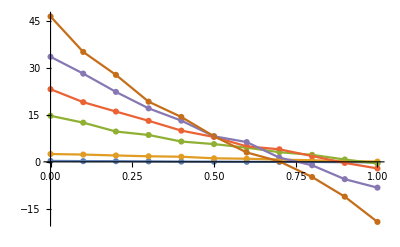

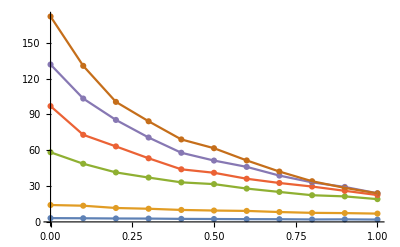

```mathematica
Show[{ListPlot@dudlAll[[1]],ListLinePlot@dudlAll[[1]]}]
Show[{ListPlot@dudlAll[[2]],ListLinePlot@dudlAll[[2]]}]
```

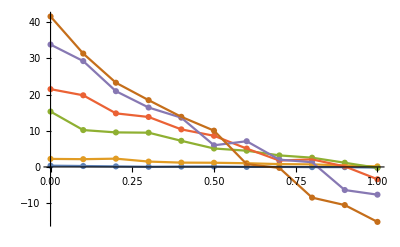

-Graphics-

```mathematica
Show[{ListPlot@dudlAll[[1]],ListLinePlot@dudlAll[[1]]}]
Show[{ListPlot@dudlAll[[2]],ListLinePlot@dudlAll[[2]]}]
```

```mathematica
dudlAllFit1=Table[Table[Fit[dudlAll[[vol]][[temp]],{1L,1},L],{temp,1,6,1}],{vol,1,2}];
dudlAllFit2=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^2,L,1},L],{temp,1,6,1}],{vol,1,2}];
dudlAllFit3=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,2}];
dudlAllFit4=Table[Table[Fit[dudlAll[[vol]][[temp]],{L^4,L^2,L^3,L^2,L,1},L],{temp,1,6,1}],{vol,1,2}];
```

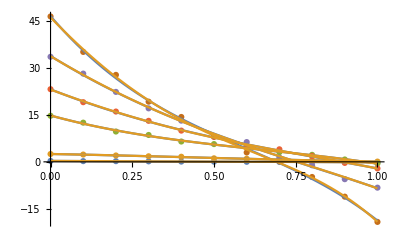

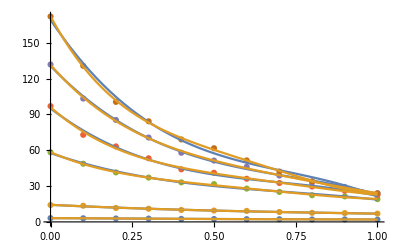

```mathematica
Show[ListPlot[dudlAll[[1]]],Plot[{dudlAllFit3[[1]],dudlAllFit4[[1]]},{L,0,1}]]
Show[ListPlot[dudlAll[[2]]],Plot[{dudlAllFit3[[2]],dudlAllFit4[[2]]},{L,0,1}]]
```

```mathematica
bound1=0;bound2=1; 

(*Solver 1 - standard *)
mvtSolver[function_]:=Solve[Evaluate@function==(Integrate[Evaluate@function,{L,a,b}/.{a->bound1,b->bound2}]/(b-a)/.{a->bound1,b->bound2})&&L∈Interval[{0,1}],L,Reals]//N
mvtSolverNum[arg_]:=mvtSolver[arg][[1]][[1]][[2]][[1]]
(*Integrator*)
dudlIntegrator[function_]:=NIntegrate[function,{L,bound1,bound2}]
(*Solver 2 - midpoint*)
midValintValMVT[fun_]:={mvtSolver[fun],
fun/.L->0.5,
dudlIntegrator[fun]}
(*Solver 3 - l1 l2 norm CS inpsired solver *)
weightedMVT[fun_,mu_,nu_,midpoint_]:=nu*NMinimize[(Evaluate[fun/.{L->mvtSolverNum[fun]}]-fun/.L->x)^2+mu*(midpoint-x)^2,x]
mvtNumWeight[arg_,mu_,nu_,midpoint_]:={mvtSolver[arg][[1]][[1]][[2]][[1]],weightedMVT[arg,mu,nu,midpoint]}
```

```mathematica
weightedMVT[dudlAllFit4[[1]][[1]],0.01,0.5]
weightedMVT[dudlAllFit4[[1]][[2]],0.01,0.5]
mvtNumWeight[dudlAllFit4[[1]][[2]],0.01,0.5]
```

weightedMVT[0.293719-0.310865 L-1.28293 L^2+2.67006 L^3-1.55222 L^4,0.01,0.5]

weightedMVT[2.50271-1.63436 L-3.47522 L^2+4.06138 L^3-1.3815 L^4,0.01,0.5]

mvtNumWeight[2.50271-1.63436 L-3.47522 L^2+4.06138 L^3-1.3815 L^4,0.01,0.5]

```mathematica
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],0.01,1,0.5],{i,1,6}]//TableForm
Table[mvtNumWeight[dudlAllFit4[[1]][[i]],200,1,0.5],{i,1,6}]//TableForm
```

0.464851 | 0.0000116122
x→0.466968
0.489813 | 1.03647×10^-6
x→0.489826
0.457792 | 0.0000178138
x→0.457795
0.457672 | 0.0000179162
x→0.457673
0.466496 | 0.0000112251
x→0.466496
0.455367 | 0.0000199208
x→0.455367

0.464851 | 0.000179859
x→0.499975
0.489813 | 0.000761515
x→0.499627
0.457792 | 0.155591
x→0.481712
0.457672 | 0.264912
x→0.468761
0.466496 | 0.199072
x→0.470297
0.455367 | 0.369329
x→0.458634

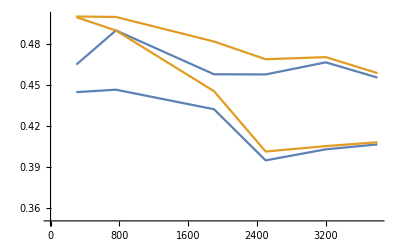

```mathematica
dataMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,2}];
dataWMVT4=Table[Table[{ttt[[i]],mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,2}];
Show[Table[ListLinePlot[{dataMVT4[[i]],dataWMVT4[[i]]},PlotRange->{{0,3800},{0.35,0.5}}],{i,1,2}]]
```

```mathematica
datafahMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,2}];
datafahWMVT4=Table[Table[{ttt[[i]],dudlAllFit4[[j]][[i]]/.L->mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,2}];
datafahMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[1]]},{i,1,6}],{j,1,2}];
datafahWMVT3=Table[Table[{ttt[[i]],dudlAllFit3[[j]][[i]]/.L->mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]]},{i,1,6}],{j,1,2}];
```

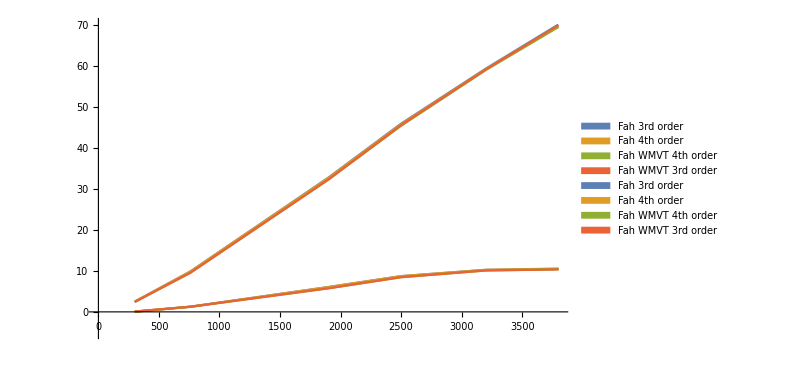

```mathematica
Show[Table[ListLinePlot[{datafahMVT3[[i]],datafahMVT4[[i]],datafahWMVT4[[i]],datafahWMVT3[[i]]},PlotRange->{{0,3800},{-5,70}},PlotLegends->SwatchLegend[{"Fah 3rd order","Fah 4th order","Fah WMVT 4th order","Fah WMVT 3rd order"}]],{i,1,2}],ImageSize->600]
```

```mathematica
Table[Table[mvtNumWeight[dudlAllFit4[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,2}]//TableForm
Table[Table[mvtNumWeight[dudlAllFit3[[j]][[i]],200,1,0.5][[2]][[2]][[1]][[2]],{i,1,6}],{j,1,2}]//TableForm
```

0.499975 | 0.499627 | 0.481712 | 0.468761 | 0.470297 | 0.458634
0.49951 | 0.489732 | 0.44544 | 0.401394 | 0.405338 | 0.408147

0.499999 | 0.49978 | 0.481384 | 0.470994 | 0.471948 | 0.467047
0.499686 | 0.489571 | 0.425016 | 0.387996 | 0.397327 | 0.388421